```mathematica
hbarc=.1973
```

0.1973

## Equation of state

```mathematica
raw=Partition[BinaryReadList[FileNameJoin[{NotebookDirectory[],"../hrg_hotqcd_eos_binary.dat"}],"Real64"],4];
epfct=Interpolation[raw[[;;,{1,2}]],InterpolationOrder->2];
Tefct=Interpolation[raw[[;;,{4,1}]],InterpolationOrder->2];
Tsfct=Interpolation[raw[[;;,{4,3}]],InterpolationOrder->2];
cs2FctPre=D[epfct[x],x]
cs2QCD[Tinfm_]:=cs2FctPre/.x->Tefct[Tinfm*hbarc]
```

InterpolatingFunction[{{0.0003894, 1903.36}}, <>][x]

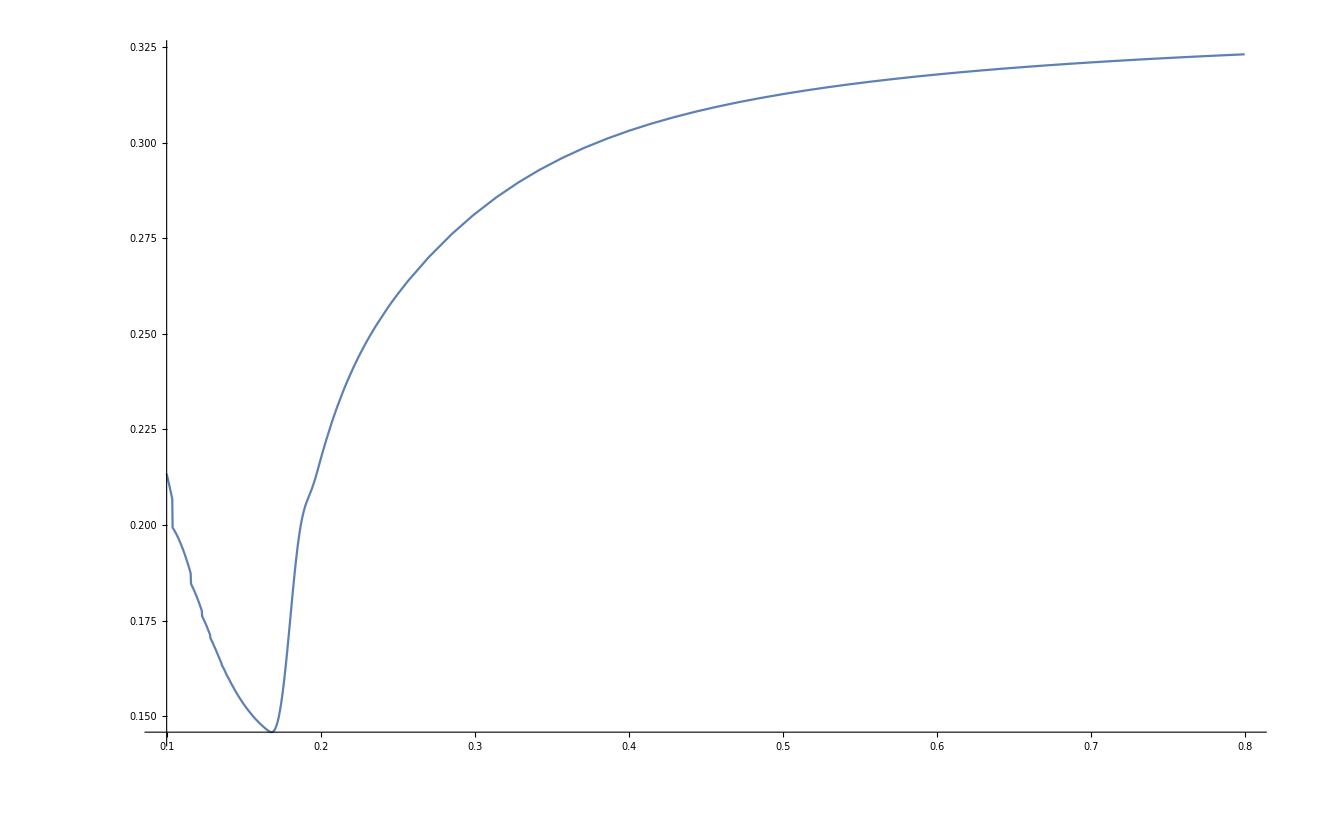

```mathematica
Plot[cs2QCD[TinMeV/hbarc],{TinMeV,.1,.8}]
```

## 2nd order Bjorken - Bulk only test

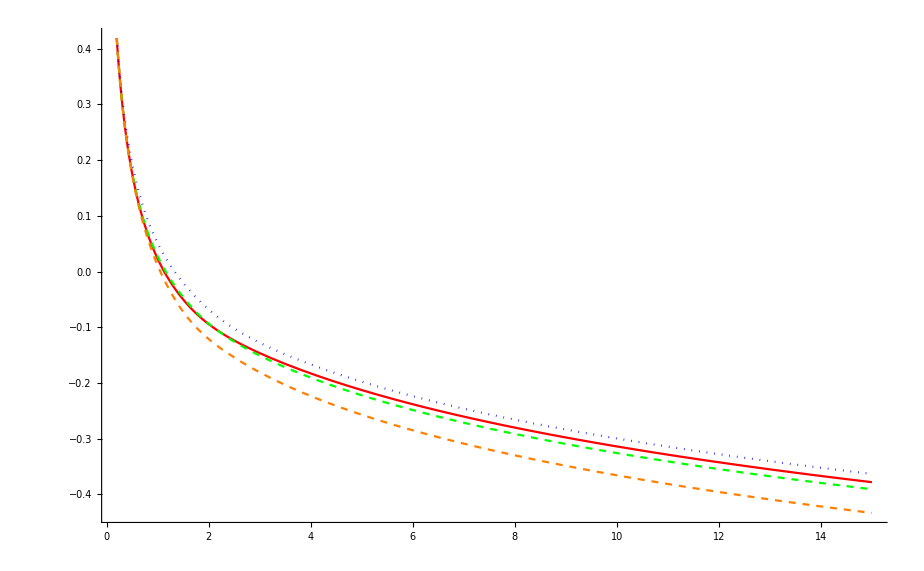

```mathematica
PiHatNS[T_,tau_]:=-zetaOverS[T]/T/tau

zetaOverS[Tinfm_]:=Module[{TinGeV=Tinfm hbarc,maxVal=0.3,width=0.03,TpeakInGeV=0.185,lambdaVal=0,diff,diffRatio},
diff=TinGeV-TpeakInGeV;
diffRatio=(diff)/(width*(lambdaVal*Sign[diff]+1));
Return[maxVal/(1+diffRatio*diffRatio)];
]
(*Plot[zetaOverS[TinGeV/hbarc],{TinGeV,.1,.5},PlotRange->All]*)
(*CPi=5.;*)
T0=.3/hbarc;
tau0=.2;
PiHat0=0 PiHatNS[T0,tau0];


cs2Fct[Tinfm_]:=cs2QCD[Tinfm]

(*tauPiFct[Tinfm_]:=zetaOverS[Tinfm]/Tinfm/(15.*(1./3-cs2Fct[Tinfm])^2)*)
tauPiFct[Tinfm_]:=1.;

(* Exact solution *)
sols=NDSolve[{
D[LogT[tau],tau]==-cs2Fct[Exp[LogT[tau]]]/tau (1+PiHat[tau]),
D[PiHat[tau],tau]==-(PiHat[tau]-(PiHatNS[Exp[LogT[tau]],tau]))/(tauPiFct[Exp[LogT[tau]]])-PiHat[tau]/tau(2/3-1-cs2Fct[Exp[LogT[tau]]]) +PiHat[tau]^2 (cs2Fct[Exp[LogT[tau]]]+1)/tau,
LogT[tau0]==Log[T0],
PiHat[tau0]==PiHat0
},
{LogT,PiHat},
{tau,tau0,100.}
];
logTsol=LogT/.sols[[1]];
PiHatsol=PiHat/.sols[[1]];


(*sols2=NDSolve[{
D[LogT[tau],tau]==-cs2Fct[Exp[LogT[tau]]]/tau (1+PiB[tau]/(Tsfct[hbarc*Exp[LogT[tau]]]*Exp[LogT[tau]])),
D[PiB[tau],tau]==-(PiB[tau]-(-zetaOverS[Exp[LogT[tau]]]*Tsfct[hbarc*Exp[LogT[tau]]]/tau))/(tauPiFct[Exp[LogT[tau]]])-2/3 PiB[tau]/tau,
LogT[tau0]==Log[T0],
PiB[tau0]==PiHat0
},
{LogT,PiB},
{tau,tau0,100.}
];
logTsol2=LogT/.sols2[[1]];
PiB2=PiB/.sols2[[1]];*)

(* Solution with approximation for PiHat (Eq. 23 of the paper) *)
solsWPiHatApprox=NDSolve[{
D[LogT[tau],tau]==-cs2Fct[Exp[LogT[tau]]]/tau (1+(ⅇ^(-(tau-tau0)/tauPiFct[Exp[LogT[tau]]]) (tau/tau0)^(2/3) (PiHat0-PiHatNS[T0,tau0])+ (PiHatNS[Exp[LogT[tau]],tau])))
,
LogT[tau0]==Log[T0]
},
{LogT},
{tau,tau0,100.}
];
logTsolsWPiHatApprox=LogT/.solsWPiHatApprox[[1]];

(*solsWPiApprox=NDSolve[{
D[LogT[tau],tau]==-cs2Fct[Exp[LogT[tau]]]/tau (1+(ⅇ^(-(tau-tau0)/tauPiFct[Exp[LogT[tau]]]) (tau0/tau)^(2/3) (PiHat0-PiHatNS[T0,tau0])+ (PiHatNS[Exp[LogT[tau]],tau])))
,
LogT[tau0]==Log[T0]
},
{LogT},
{tau,tau0,100.}
];
logTsolsWPiApprox=LogT/.solsWPiApprox[[1]];*)

(* Navier-Stokes solution *)
solsNS=NDSolve[{
D[LogT[tau],tau]==-cs2Fct[Exp[LogT[tau]]]/tau (1+PiHatNS[Exp[LogT[tau]],tau])
,
LogT[tau0]==Log[T0]
},
{LogT},
{tau,tau0,100.}
];
logTsolsNS=LogT/.solsNS[[1]];

(* Ideal solution *)
solsIdeal=NDSolve[{
D[LogT[tau],tau]==-cs2Fct[Exp[LogT[tau]]]/tau 
,
LogT[tau0]==Log[T0]
},
{LogT},
{tau,tau0,100.}
];
logTsolsIdeal=LogT/.solsIdeal[[1]];

(* Plot of Pi-hat: exact vs approximation *)
(*Plot[{PiB2[tau]/(Tsfct[hbarc*Exp[logTsol2[tau]]] *Exp[logTsol2[tau]]),PiHatsol[tau],(ⅇ^(-(tau-tau0)/tauPiFct[Exp[logTsolsWPiHatApprox[tau]]]) (tau/tau0)^(2/3) (PiHat0-PiHatNS[T0,tau0])+ (PiHatNS[Exp[logTsolsWPiHatApprox[tau]],tau])),(ⅇ^(-(tau-tau0)/tauPiFct[Exp[logTsolsWPiApprox[tau]]]) (tau0/tau)^(2/3) (PiHat0-PiHatNS[T0,tau0])+ (PiHatNS[Exp[logTsolsWPiApprox[tau]],tau]))},{tau,tau0,15.},PlotStyle->{Red,Directive[Green,Dashed],Directive[Blue,Dotted],Directive[Orange,Dashed]},PlotRange->All]*)
Plot[{logTsol[tau],logTsolsWPiHatApprox[tau],logTsolsNS[tau],logTsolsIdeal[tau]},{tau,tau0,15.},PlotStyle->{Red,Directive[Green,Dashed],Directive[Blue,Dotted],Directive[Orange,Dashed]},PlotRange->All]
```

```mathematica
(* Plot of temperature: exact vs approximation *)
(*Plot[{PiHatsol[tau],(ⅇ^(-(tau-tau0)/tauPiFct[Exp[logTsolsWPiHatApprox[tau]]]) (tau/tau0)^(2/3) (PiHat0-PiHatNS[T0,tau0])+ (PiHatNS[Exp[logTsolsWPiHatApprox[tau]],tau])),(ⅇ^(-(tau-tau0)/tauPiFct[Exp[logTsolsWPiApprox[tau]]]) (tau0/tau)^(2/3) (PiHat0-PiHatNS[T0,tau0])+ (PiHatNS[Exp[logTsolsWPiApprox[tau]],tau]))},{tau,tau0,15.},PlotStyle->{Red,Directive[Green,Dashed],Directive[Blue,Dotted],Directive[Orange,Dashed]},PlotRange->All]*)
```

## Pi-hat: approximate solution

```mathematica
(*assumptions1=0<cs2Bar<1/3&&tau>0&&tauPi>0&&PiHat0∈Reals;
pre1=DSolve[{D[PiHat[tau],tau]==-(PiHat[tau]-PiHatNS[tau])/tauPi+PiHat[tau]/tau(-2/3+1+cs2Bar),PiHat[tau0]==PiHat0} ,PiHat[tau],tau,Assumptions->assumptions1];
FullSimplify[pre1,assumptions1]*)
```

{{PiHat[tau]→ⅇ^(-tau/tauPi) (tau0/tau)^(-1/3-cs2Bar) (ⅇ^(tau0/tauPi) PiHat0+tau0^(1/3+cs2Bar) ((ⅇ^(K[1]/tauPi) K[1]^(-1/3-cs2Bar) PiHatNS[K[1]])/tauPiK[1]1tau-(ⅇ^(K[1]/tauPi) K[1]^(-1/3-cs2Bar) PiHatNS[K[1]])/tauPiK[1]1tau0))}}

```mathematica
PiHatApprox1[T_,tau_?NumericQ,tauPi_?NumericQ,tau0_?NumericQ,cs2Bar_?NumericQ,PiHat0_?NumericQ]:=ⅇ^(-tau/tauPi) (tau0/tau)^(-1/3-cs2Bar) (ⅇ^(tau0/tauPi) PiHat0+tau0^(1/3+cs2Bar) NIntegrate[Exp[taup/tauPi](tau0/taup)^(1/3+cs2Bar)/tauPi PiHatNS[T[taup],taup],{taup,tau0,tau},PrecisionGoal->4])
```

```mathematica
PiHatApprox2[T_,tau_?NumericQ,tauPi_?NumericQ,tau0_?NumericQ,cs2Bar_?NumericQ,PiHat0_?NumericQ]:=ⅇ^(-(tau-tau0)/tauPi) (tau/tau0)^(1/3+cs2Bar) (PiHat0-PiHatNS[T[tau0],tau0])+PiHatNS[T[tau],tau]
```

```mathematica
With[{tau=1.,tmpTauPi=1.},{-1/tau PiHatsol[tau],-1/tau PiHatApprox1[Function[u,Exp[logTsol[u]]],tau,tmpTauPi,tau0,1/4,PiHat0],-1/tau PiHatApprox2[Function[u,Exp[logTsol[u]]],tau,tmpTauPi,tau0,1/4,PiHat0],-1/tau PiHatNS[Exp[logTsol[tau]],tau]}]
```

{0.109641,0.0446715,0.150225,0.222443}

```mathematica
(*tmpTauPi=tauPiFct[1.];
Plot[{-1/tau PiHatsol[tau],-1/tau PiHatApprox1[Function[u,Exp[logTsol[u]]],tau,tmpTauPi,tau0,1/4,PiHat0],-1/tau PiHatApprox2[Function[u,Exp[logTsol[u]]],tau,tmpTauPi,tau0,1/4,PiHat0],-1/tau PiHatNS[Exp[logTsol[tau]],tau]},{tau,tau0,5.},PlotRange->All,PlotStyle->{Red,Directive[Green,Dashed],Directive[Blue,Dotted],Directive[Orange,Dashed]}]
Clear[tmpTauPi]*)
```

## Effective viscosity

```mathematica
isEffVisc[tau_]:=NIntegrate[cs2QCD[Exp[logTsol[taup]]]/taup PiHatsol[taup],{taup,tau0,tau},AccuracyGoal->3]/NIntegrate[cs2QCD[Exp[logTsol[taup]]]/taup^2 1/Exp[logTsol[taup]],{taup,tau0,tau},AccuracyGoal->3]
```

```mathematica
isEffVisc2[T_]:=NIntegrate[1/Tp  PiHatsol[tau0(T0/Tp)^(1/cs2QCD[Sqrt[Tp T0]])],{Tp,T,T0},AccuracyGoal->3]/NIntegrate[1/Tp^2 1/tau0 (Tp/T0)^(1/cs2QCD[Sqrt[Tp T0]]),{Tp,T,T0},AccuracyGoal->3]
```

```mathematica
(*FullSimplify[ⅇ^(-(tau0(T0/Tp)^(1/cs2Bar)-tau0)/tauPi) ((tau0(T0/Tp)^(1/cs2Bar))/tau0)^(1/3+cs2Bar) (PiHat0-PiHatNST0)+PiHatNST,Assumptions->0<cs2Bar<1/3&&tau>0&&tauPi>0&&PiHat0∈Reals&&T0>Tp>0&&tau>tau0>0&&tauPi>0]*)
```

```mathematica
isEffVisc3[T_,cs2Bar_]:=With[{tauPi=tauPiFct[1.]},NIntegrate[1/Tp  (PiHatNS[Tp,tau0(T0/Tp)^(1/cs2Bar)]+ⅇ^((tau0(1- (T0/Tp)^(1/cs2Bar)))/tauPi) (PiHat0-PiHatNS[T0,tau0]) (T0/Tp)^(1+1/(3 cs2Bar))),{Tp,T,T0},AccuracyGoal->3]/NIntegrate[1/Tp^2 1/tau0 (Tp/T0)^(1/cs2Bar),{Tp,T,T0},AccuracyGoal->3]]
```

```mathematica
(*isEffVisc3b[T_]:=With[{tauPi=tauPiFct[1.]},NIntegrate[1/Tp  (PiHatNS[Tp,tau0(T0/Tp)^(1/cs2QCD[Sqrt[Tp T0]])]+ⅇ^((tau0(1- (T0/Tp)^(1/cs2QCD[Sqrt[Tp T0]])))/tauPi) (PiHat0-PiHatNS[T0,tau0]) (T0/Tp)^(1+1/(3 cs2QCD[Sqrt[Tp T0]]))),{Tp,T,T0},AccuracyGoal->3]/NIntegrate[1/Tp^2 1/tau0 (Tp/T0)^(1/cs2QCD[Sqrt[Tp T0]]),{Tp,T,T0},AccuracyGoal->3]]*)
```

```mathematica
PiHatNS[Tp]
```

```mathematica
isEffVisc[1.]
isEffVisc[2.]
isEffVisc[5.]
isEffVisc[10.]
```

-0.0163165

-0.0383943

-0.0569191

-0.060248

```mathematica
isEffVisc2[Exp[logTsol[1.]]]
isEffVisc2[Exp[logTsol[2.]]]
isEffVisc2[Exp[logTsol[5.]]]
isEffVisc2[Exp[logTsol[10.]]]
```

-0.0146024

-0.0309764

-0.0510376

-0.0615574

```mathematica
isEffVisc3b[Exp[logTsol[1.]]]
isEffVisc3b[Exp[logTsol[2.]]]
isEffVisc3b[Exp[logTsol[5.]]]
isEffVisc3b[Exp[logTsol[10.]]]
```

-0.0254951

-0.045552

-0.0543947

-0.0563286

```mathematica
isEffVisc3[Exp[logTsol[1.]],1/5]
isEffVisc3[Exp[logTsol[2.]],1/5]
isEffVisc3[Exp[logTsol[5.]],1/5]
isEffVisc3[Exp[logTsol[10.]],1/5]
```

-0.0153688

-0.0323756

-0.0414617

-0.0439738

```mathematica
isEffVisc3[Exp[logTsol[1.]],1/3]
isEffVisc3[Exp[logTsol[2.]],1/3]
isEffVisc3[Exp[logTsol[5.]],1/3]
isEffVisc3[Exp[logTsol[10.]],1/3]
```

-0.0334674

-0.0599696

-0.0706678

-0.0700136

```mathematica
isEffVisc3[Exp[logTsol[1.]],1/4]
isEffVisc3[Exp[logTsol[2.]],1/4]
isEffVisc3[Exp[logTsol[5.]],1/4]
isEffVisc3[Exp[logTsol[10.]],1/4]
```

-0.0235608

-0.0440787

-0.0535565

-0.0553817

-0.0153688

-0.0323756

-0.0414617

-0.0439738

## Example

```mathematica
isEffViscPre4[T_,cs2Bar_]:=With[{tauPi=tauPiFct[1.]},NIntegrate[1/Tp  (PiHatNS[Tp,tau0(T0/Tp)^(1/cs2Bar)]+ⅇ^((tau0(1- (T0/Tp)^(1/cs2Bar)))/tauPi) (PiHat0-PiHatNS[T0,tau0]) (T0/Tp)^(1+1/(3 cs2Bar))),{Tp,T,T0},AccuracyGoal->3]/NIntegrate[1/Tp^2 1/tau0 (Tp/T0)^(1/cs2Bar),{Tp,T,T0},AccuracyGoal->3]]
isEffVisc4[T_,cs2Bar_]:=With[{tauPi=tauPiFct[1.]},NIntegrate[1/Tp  (PiHatNS[Tp,tau0(T0/Tp)^(1/cs2Bar)]+ⅇ^((tau0(1- (T0/Tp)^(1/cs2Bar)))/tauPi) (PiHat0-PiHatNS[T0,tau0]) (T0/Tp)^(1+1/(3 cs2Bar))),{Tp,T,T0},AccuracyGoal->3]/NIntegrate[1/Tp^2 1/tau0 (Tp/T0)^(1/cs2Bar),{Tp,T,T0},AccuracyGoal->3]]
```

```mathematica
assumptions1=0<cs2Bar<1/3&&tau>0&&tauPi>0&&PiHat0∈Reals
```

0<cs2Bar<1/3&&tau>0&&tauPi>0&&PiHat0∈ℝ

```mathematica
denum=Integrate[1/Tp^2 1/tau0 (Tp/T0)^(1/cs2Bar),{Tp,T,T0},Assumptions->T0>T>0]
```

(cs2Bar T-cs2Bar (T/T0)^(1/cs2Bar) T0)/(T T0 tau0-cs2Bar T T0 tau0)

```mathematica
num=Integrate[1/Tp  (ⅇ^((tau0(1- (T0/Tp)^(1/cs2Bar)))/tauPi)  (T0/Tp)^(1+1/(3 cs2Bar))),{Tp,T,T0},Assumptions->assumptions1]
```

Integrate[(ⅇ^((tau0 (1-(T0/Tp)^(1/cs2Bar)))/tauPi) (T0/Tp)^(1+1/(3 cs2Bar)))/Tp,{Tp,T,T0},Assumptions→0<cs2Bar<1/3&&tau>0&&tauPi>0&&PiHat0∈ℝ]